## §3. Применение операционного исчисления

### 3.1. Решение линейных дифференциальных уравнений и систем уравнений с постоянными коэффициентами.

Для того чтобы найти решение x(t) линейного дифференциального уравнения с постоянными коэффициентами

x^(n)+a_1 x^(n-1)+...+a_n x=f(t)

(где f(t) - оригинал), удовлетворяющее начальным условиям

x(0)=x_0,x'(0)=(x')_0,...,x^(n-1)(0)=(x^(n-1))_0

следует применить к обеим частям этого уравнения преобразование Лапласа, т.е. от уравнения (1) с условиями (2) перейти к операторному уравнению

(p^n+a_1 p^(n-1)+...+a_n)X(p)+Q(p)=F(p),

где X(p)- изображение искомого решения, F(p)- изображение функции f(t), а Q(p) - некоторый многочлен, коэффициенты которого зависят от начальных данных (2) и который тождественно равен нулю, если x_0=(x')_0=...=(x^(n-1))_0=0. Решим операторное уравнение относительно X(p):

X(p)=(F(p)-Q(p))/(L(p))

L(p)=p^n+a_1 p^(n-1)+...+a_n- характеристический многочлен

и найдя оригинал для X(p), мы получим искомое решение x(t). Если считать x_0,(x')_0,...,(x^(n-1))_0 произвольными постоянными, то найденное решение будет общим решением уравнения (1). Совершенно аналогично решаются и системы линейных дифференциальных уравнений с постоянными коэффициентами. Отличие будет лишь в том, что вместо одного операторного уравнения мы получим систему таких уравнений, которые будут линейными относительно изображений искомых функций.

##### Пример №13.105

Найти общее решение дифференциального уравнения:

x''+9x=cos 3t

Найдем изображение этого уравнения при помощи модуля laplaceD из Главы 3 Параграфа 1:

```mathematica
dif=laplaceD[t,x''[t]+9x[t]==Cos[3t],{}]
```

-p x[0]+(9+p^2) X[p]-x'[0]==p/(9+p^2)

Мы получили изображение исходного уравнения, выразим в нём искомую функцию X(p):

```mathematica
Solve[dif,X[p]]
```

{{X[p]→(p+9 p x[0]+p^3 x[0]+9 x'[0]+p^2 x'[0])/((9+p^2)^2)}}

Выше мы нашли выражение для изображения искомой функции, теперь найдем саму функцию:

```mathematica
InverseLaplaceTransform[(p+9 p x[0]+p^3 x[0]+9 x'[0]+p^2 x'[0])/((9+p^2)^2),p,t]
```

1/6 (t Sin[3 t]+6 Cos[3 t] x[0]+2 Sin[3 t] x'[0])

Итак, мы получили решение дифференциального уравнения:

x(t)=1/6 (2 sin(3 t) x'(0)+6 x(0) cos(3 t)+t sin(3 t))

Обозначив начальные условия x(0)=C_1, x'(0)/3=C_2, получим общее решение в привычной форме:

x(t)=С_1 cos(3 t)+С_2 sin(3 t) +1/6 t sin(3 t)

##### Пример №13.111

Найти решение дифференциального уравнения при заданных начальных условиях:

x''+2x'+x=ⅇ^-t,x(0)=1,x'(0)=0

Найдем изображение:

```mathematica
dif=laplaceD[t,x''[t]+2x'[t]+x[t]==Exp[-t],{x[0]-> 1,x'[0]-> 0}]
```

-2-p+(1+2 p+p^2) X[p]==1/(1+p)

Получим выражение для изображения:

```mathematica
Solve[dif,X[p]]
```

{{X[p]→(3+3 p+p^2)/(1+p)^3}}

Теперь найдем решение:

```mathematica
InverseLaplaceTransform[(3+3 p+p^2)/(1+p)^3,p,t]
```

1/2 ⅇ^-t (2+2 t+t^2)

Решение исходного дифференциального уравнения:

x(t)=1/2 ⅇ^-t (2+2 t+t^2)

##### Программный модуль

Составим простой программный модуль для решения дифференциального уравнения:

```mathematica
dsolve[t_,expr_,rule_]:=Module[{im,xp},
im=LaplaceTransform[expr,t,p]/.LaplaceTransform[x[t],t,p]-> X[p]/.rule;
xp=X[p]/.Flatten@Solve[im,X[p]];
InverseLaplaceTransform[xp,p,t]//Simplify
]
```

##### Пример №13.117

Найти решение дифференциального уравнения:

x^IV-x=sh t, x(0)=x'(0)=x''(0)=0,   x'''(0)=1

Решим задачу при помощи созданного нами модуля:

```mathematica
dsolve[t,x''''[t]-x[t]==Sinh[t],{x[0]-> 0,x'[0]-> 0,x''[0]-> 0,x'''[0]-> 1}]//FullSimplify
```

1/4 (t Cosh[t]-Sin[t])

Итак, получаем ответ:

x(t)=1/4(t ch(t)-sin(t))

##### Пример №13.121

Найти при нулевых начальных условиях решение следующего дифференциального уравнения:

x''+x'=f(t), где f(t)=Piecewise[{{cos t, 0≤t<π}, {0, t≥ π}}]

Сначала запишем функцию f(t):

```mathematica
f[t_]:=Piecewise[{{Cos[t],0≤t<π},{0,t≥ π}}]
```

Теперь найдем решение:

```mathematica
dsolve[t,x''[t]+x'[t]==f[t],{x[0]-> 0,x'[0]-> 0}]//FullSimplify
```

1/2 ⅇ^-t (1+ⅇ^π HeavisideTheta[-π+t]+ⅇ^t (-1+HeavisideTheta[-π+t]) (Cos[t]-Sin[t]))

Таким образом, ответ:

x(t)=1/2 ⅇ^-t (ⅇ^π H(t-π)+ⅇ^t (H(t-π)-1) (cos(t)-sin(t))+1),

Теперь рассмотрим решение систем дифференциальных уравнений.

##### Пример №13.129

Найти общее решение системы дифференциальных уравнений:

Piecewise[{{x''+y'=t, }, {y''-x'=0, }}]

Принцип решения не изменился: находим изображение системы дифференциальных уравнений, затем решение для функции-изображения, а потом саму функцию-оригинал.

Чтобы найти изображение системы применим функцию LaplaceTransofrorm, которая обладает атрибутом Listable, то есть  применяется для каждого элемента списка.

```mathematica
LaplaceTransform[{x''[t]+y'[t]==t,y''[t]-x'[t]==0},t,p]
```

{p^2 LaplaceTransform[x[t],t,p]+p LaplaceTransform[y[t],t,p]-p x[0]-y[0]-x'[0]==1/p^2,-p LaplaceTransform[x[t],t,p]+p^2 LaplaceTransform[y[t],t,p]+x[0]-p y[0]-y'[0]==0}

Получили систему уравнений изображений. Произведем необходимую замену:

```mathematica
dif=LaplaceTransform[{x''[t]+y'[t]==t,y''[t]-x'[t]==0},t,p]/.{LaplaceTransform[x[t],t,p]->X[p],LaplaceTransform[y[t],t,p]->Y[p]}
```

{-p x[0]+p^2 X[p]-y[0]+p Y[p]-x'[0]==1/p^2,x[0]-p X[p]-p y[0]+p^2 Y[p]-y'[0]==0}

Теперь необходимо решить уравнения относительно X(p) и Y(p):

```mathematica
Solve[dif,{X[p],Y[p]}]
```

{{X[p]→-(-1-p x[0]-p^3 x[0]-p^2 x'[0]+p y'[0])/(p^2 (1+p^2)),Y[p]→-(-1-p^2 y[0]-p^4 y[0]-p^2 x'[0]-p^3 y'[0])/(p^3 (1+p^2))}}

а также найти выражения для функций оригиналов:

```mathematica
InverseLaplaceTransform[-(-1-p x[0]-p^3 x[0]-p^2 x'[0]+p y'[0])/(p^2 (1+p^2)),p,t]
InverseLaplaceTransform[-(-1-p^2 y[0]-p^4 y[0]-p^2 x'[0]-p^3 y'[0])/(p^3 (1+p^2)),p,t]
```

t-Sin[t]+x[0]+Sin[t] x'[0]-y'[0]+Cos[t] y'[0]

-1+t^2/2+Cos[t]+y[0]+x'[0]-Cos[t] x'[0]+Sin[t] y'[0]

где x(0),y(0),x'(0),y'(0)  - произвольные константы.

Решение системы:

x(t)=sin(t) x'(0)+cos(t) y'(0)+t-sin(t)+x(0)-y'(0)
y(t)=t^2/2-cos(t) x'(0)+sin(t) y'(0)+cos(t)+x'(0)+y(0)-1

##### Пример №13.133

Найти решение системы дифференциальных уравнений при заданных начальных условиях:

Piecewise[{{x''-y'=0, }, {x-y''=2sin t, }}], x(0)=-1,x'(0)=y(0)=y'(0)=1

Запишем список начальных условий:

```mathematica
cond={x[0]-> -1,y'[0]->1,y[0]->1,x'[0]-> 1};
```

Найдем изображение системы:

```mathematica
dif=LaplaceTransform[{x''[t]-y'[t]==0,x[t]-y''[t]==2Sin[t]},t,p]/.{LaplaceTransform[x[t],t,p]->X[p],LaplaceTransform[y[t],t,p]->Y[p]}/.cond
```

{p+p^2 X[p]-p Y[p]==0,1+p+X[p]-p^2 Y[p]==2/(1+p^2)}

Найдем решение относительно функций оригиналов:

```mathematica
Solve[dif,{X[p],Y[p]}]
```

{{X[p]→-(-1+p)/(1+p^2),Y[p]→-(-1-p)/(1+p^2)}}

Теперь можно получить решение исходной системы:

```mathematica
InverseLaplaceTransform[-(-1+p)/(1+p^2),p,t]
InverseLaplaceTransform[-(-1-p)/(1+p^2),p,t]
```

-Cos[t]+Sin[t]

Cos[t]+Sin[t]

Таким образом, ответ:

x(t)=-cos(t)+sin(t)
y(t)=cos(t)+sin(t)

##### Программный модуль

Мы можем составить программный модуль для решения систем дифференциальных уравнений с двумя неизвестными функциями:

```mathematica
dssolve[t_,expr_,rules_]:=Module[{zam,im,sol},
zam={LaplaceTransform[x[t],t,p]->X[p],LaplaceTransform[y[t],t,p]->Y[p]};
im=LaplaceTransform[expr,t,p]/.zam/.rules;
sol=Flatten@Solve[im,{X[p],Y[p]}];
Print["x[t]=" ,Simplify@InverseLaplaceTransform[X[p]/.sol,p,t]];
Print["y[t]=" ,Simplify@InverseLaplaceTransform[Y[p]/.sol,p,t]];]
```

Рассмотрим пример работы:

##### Пример №13.135

Найти решение системы дифференциальных уравнений при заданных начальных условиях:

Piecewise[{{x''-y'=ⅇ^t, }, {x'+y''-y=0, }}], x(0)=1,y(0)=-1,x'(0)=y'(0)=0

Воспользуемся только что написанным модулем для поиска решения:

```mathematica
dssolve[t,{x''[t]-y'[t]==Exp[t],x'[t]+y''[t]-y[t]==0},{x[0]->1,y[0]->-1,x'[0]->0,y'[0]->0}]
```

x[t]= (1+t^2/2)

y[t]= (-ⅇ^t+t)

Получили ответ:

x(t)=1+t^2/2

y(t)=-e^t+t

##### Пример №13.137

Проинтегрировать при нулевых начальных условиях систему дифференциальных уравнений:

Piecewise[{{x''-y'=f_1(t), }, {y'+x=f_2(t), }}], f_1(t)=Piecewise[{{1, 0≤ t<π}, {0, t≥ π}}], f_2(t)=Piecewise[{{t, 0≤ t<π/2}, {π-t, π/2≤t<π}, {0, t≥ π}}]

Запишем функции f_1 и f_2:

```mathematica
f1[t_]:=Piecewise[{{1,0≤t<Pi}}]
f2[t_]:=Piecewise[{{t,0≤ t<Pi/2},{Pi-t,Pi/2≤t<Pi}}]
```

Получим их графики:

```mathematica
Plot[{f1[t],f2[t]},{t,-1,4}]
```

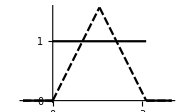

Теперь можно найти решение:

```mathematica
dssolve[t,{x''[t]-y'[t]==f1[t],x[t]+y'[t]==f2[t]},{x[0]->0,y[0]->0,x'[0]->0,y'[0]->0}]
```

x[t]= (1+t-Cos[t]+(π-2 t-2 Cos[t]) HeavisideTheta[-π/2+t]-Sin[t]+HeavisideTheta[-π+t] (-1-π+t-Cos[t]+Sin[t]))

y[t]= (1-t-Cos[t]+2 HeavisideTheta[-π/2+t] (-1+Sin[t])+Sin[t]+HeavisideTheta[-π+t] (1-π+t+Cos[t]+Sin[t]))

Примечание: можно было бы составить модуль для решения систем с произвольным количеством неизвестных функций, но это  слишком трудоемко и выходит за рамки данного курса.

### 3.2. Решение линейных интегральных и интегро-дифференциальных уравнений.

Используя теорему свертывания, можно легко найти изображения решений интегральных уравнений Вольтерра 1-ого и 2-ого рода в том случае, когда ядром в соответствующем уравнении служит функция вида K(t-τ), где K(t) - оригинал. Этот метод применим и к интегро-дифференциальных уравнениям с таким же ядром.

##### Пример №13.139

Решить следующее интегральное уравнение:

∫_0^t ch(t-τ)x(τ)ⅆτ=ch t - cos t

Метод решения подобных уравнений ничем не отличается от рассмотренного ранее метода решения дифференциальных уравнений.

Напомним, что по теореме свертывания:

∫_0^t f(t-τ)x(τ)ⅆτ=(f*x )(t)≐F(p)·X(p)

Найдем изображение исходного уравнения:

```mathematica
LaplaceTransform[Integrate[Cosh[t-τ]x[τ],{τ,0,t}]==Cosh[ t] - Cos [t],t,p]
```

(p LaplaceTransform[x[t],t,p])/(-1+p^2)==p/(-1+p^2)-p/(1+p^2)

Как и раньше, обозначим LaplaceTransform[x[t],t,p] как X[p].

```mathematica
dif=LaplaceTransform[Integrate[Cosh[t-τ]x[τ],{τ,0,t}]==Cosh[ t] - Cos [t],t,p]/.LaplaceTransform[x[t],t,p]->X[p]
```

(p X[p])/(-1+p^2)==p/(-1+p^2)-p/(1+p^2)

Теперь из этого уравнения необходимо выразить функцию X(p):

```mathematica
Solve[dif,X[p]]
```

{{X[p]→2/(1+p^2)}}

Зная выражение для изображения, найдем функцию-решение исходного интегрального уравнения:

```mathematica
InverseLaplaceTransform[2/(1+p^2),p,t]
```

2 Sin[t]

Итак, ответ:

x(t)=2sin t

Если посмотреть внимательно, то можно убедиться, что последовательность действий, примененная для решения интегрального уравнения, полностью совпадает с последовательностью решения дифференциальных уравнений, следовательно, мы можем воспользоваться написанным нами ранее модулем dsolve с пустыми начальными условиями. Убедимся в этом:

```mathematica
dsolve[t,Integrate[Cosh[t-τ]x[τ],{τ,0,t}]==Cosh[ t] - Cos [t],{}]
```

2 Sin[t]

Получили, как и ожидалось, тот же самый ответ. Следовательно, данный модуль можно в каком-то роде назвать универсальным.

##### Пример №13.141

Решить интегро-дифференциальное уравнение:

∫_0^t ⅇ^(t-τ)sin(t-τ)x(τ)ⅆτ=x''-x'+ⅇ^t(1-cos t), x(0)=x'(0)=1

Данное уравнение содержит и интеграл и дифференциал неизвестной функции, поэтому называется интегро-дифференциальным уравнением.

Однако, способ решения и такого уравнения ничем не отличается от рассмотренного ранее.

Поэтому воспользуемся модулем dsolve:

```mathematica
dsolve[t,Integrate[Exp[t-τ]Sin[t-τ]x[τ],{τ,0,t}]==x''[t]-x'[t]+Exp[t](1-Cos[t]),{x[0]->1,x'[0]->1}]
```

ⅇ^t

Убедимся, что полученный ответ верен, подставив полученную функцию в исходное уравнение:

```mathematica
Integrate[Exp[t-τ]Sin[t-τ]x[τ],{τ,0,t}]==D[x[t],{x,2}]-D[x[t],x]+Exp[t](1-Cos[t])/.x[t_]->Exp[t]
```

-ⅇ^t (-1+Cos[t])==ⅇ^t (1-Cos[t])

Функция удовлетворяет уравнению, следовательно получено верное решение.

Ответ:

x(t)=ⅇ^t

##### Пример №13.143

Проинтегрировать уравнение Абеля:

∫_0^t (x(τ))/(√(t-τ))ⅆτ==π

Разумеется, и данное уравнение входит в класс задач, решаемых с помощью функции dsolve. Воспользуемся ей:

```mathematica
dsolve[t,Integrate[x[τ](t-τ)^(-1/2),{τ,0,t}]==Pi,{}]
```

1/(√t)

Получили, что решением уравнения Абеля является функция:

x(t)=1/(√t)

Выполним проверку, подставив эту функцию в исходное уравнение:

```mathematica
Integrate[x[τ](t-τ)^(-1/2),{τ,0,t}]==Pi/.x[t_]->1/√t
```

ConditionalExpression[True,Re[t]>0&&Im[t]==0]

Получили верное равенство при условии, что действительная часть t больше нуля, а мнимая часть равна нулю.

Следует сказать, что данное уравнение является частным случаем следующего:

##### Пример №13.144

Проинтегрировать уравнение Абеля:

∫_0^t (x(τ))/(t-τ)^α ⅆτ==t^β, 0≤ α<1,  β>-1

Решим его с помощью функции dsolve:

```mathematica
dsolve[t,Integrate[x[τ](t-τ)^-α,{τ,0,t}]==t^β,{}]
```

(t^(-1+α+β) Gamma[1+β])/(Gamma[1-α] Gamma[α+β])

Решение запишем в традиционной форме:

x(t)=(Г(1+β))/(Г(1-α))t^(-1+α+β)/(Г(α+β))

где Г(t) - гамма-функция.

Убедимся в правильности решения:

```mathematica
Integrate[x[τ](t-τ)^-α,{τ,0,t}]==t^β/.x[t_]-> (t^(-1+α+β) Gamma[1+β])/(Gamma[1-α] Gamma[α+β])
```

ConditionalExpression[True,Re[α]<1&&Re[α+β]>0&&Re[t]>0&&Im[t]==0]

Оно верно при α<1, a+β>0 или β>-1, что полностью совпадает с условиями задачи.

### 3.3. Вычисление несобственных интегралов.

Один из способов вычисления несобственных интегралов вида ∫_0^∞ f(t)ⅆt основан на применении теоремы операционного исчисления о связи “конечного” значения оригинала и “начального” значения изображения. Докажем эту теорему:

Теорема:

Если f(t)≐F(p) и существует конечный предел lim_(t→+∞) f(t)=f(+∞), то

f(+∞)=lim_(p→0) p F(p)

Доказательство:

Воспользуемся теоремой подобия:

f(a t)≐1/a F(p/a)

Значению f(+∞) соответствует:

lim_(a→∞) f(a t)=f(+∞)

Тогда, согласно теореме подобия, получим:

lim_(a→+∞) f(a t)=f(+∞)=lim_(a→+∞) 1/a F(p/a)

введем обозначение :p=p/a, тогда:

lim_(a→+∞) 1/a F(p/a)=lim_(p→+0) p F(p)

Отсюда:

f(+∞)=lim_(p→+0) p F(p)

Из этой теоремы и соотношения:

∫_0^t f(t)ⅆt=1/p F(p)

при условии сходимости интеграла следует соотношение:

∫_0^(+∞) f(t)ⅆt=F(0)

##### Пример №13.150

Вычислить несобственный интеграл:

∫_0^(+∞) t^μ ⅇ^(-α t)ln tⅆt, α,μ>-1

Сначала попробуем напрямую посчитать значения данного интеграла, используя функцию Integrate:

```mathematica
Integrate[t^μ Exp[-α t]Log[t],{t,0,Infinity},Assumptions->α>0&&μ>-1]
```

-α^(-1-μ) μ Gamma[μ] (EulerGamma-HarmonicNumber[μ]+Log[α])

Время затраченное на вычисление данного интеграла очень велико (около 10 минут). Из этого можно сделать вывод, что использование вспомогательного метода описанного выше вполне рационально, и даже необходимо.

Найдем изображение подынтегральной функции с помощью LaplaceTransform:

```mathematica
i=LaplaceTransform[t^μ Exp[-α t]Log[t],t,p]
```

-(p+α)^(-1-μ) μ Gamma[μ] (EulerGamma-HarmonicNumber[μ]+Log[p+α])

EulerGamma- постоянная Эйлера, численно равная γ≃0.577216; HarmonicNumber[μ] функция гармонического числа, которая задается:

HarmonicNumber[μ]=H_μ=∑_(i=1)^μ 1/i

Итак, мы получили изображение подынтегральной функции. Теперь, чтобы получить значение несобственного интеграла, просто подставим p=0:

```mathematica
i/.p->0
```

-α^(-1-μ) μ Gamma[μ] (EulerGamma-HarmonicNumber[μ]+Log[α])

Данный ответ сходится с тем, что мы получили, воспользовавшись функцией Integrate.

Пусть функции

f(t,u) и ψ(t,u)=∫_0^(+∞) ϕ(u)f(t,u)ⅆu

являются оригиналами. Тогда, применяя теорему об интегрировании по параметру, будем иметь:

ψ(t)≐Ψ(p)=∫_0^(+∞) ϕ(u)F(p,u)ⅆu

Поэтому, если интеграл определяющий Ψ(p), можно вычислить, то для отыскания интеграла ψ(t) достаточно найти оригинал для Ψ(p),т.е.

∫_0^(+∞) ϕ(u)f(t,u)ⅆu≐∫_0^(+∞) ϕ(u)F(p,u)ⅆu

##### Пример №13.152

Вычислить несобственный интеграл:

∫_0^(+∞) ⅇ^(-t u^2)ⅆu

В данной задаче имеем:

ϕ(u)=1, f(t,u)=ⅇ^(-t u^2)

Чтобы вычислить значение интеграла, найдем изображение функции f:

```mathematica
LaplaceTransform[Exp[-t u^2],t,p]
```

1/(p+u^2)

Теперь найдем значение следующего интеграла:

Ψ(p)=∫_0^(+∞) 1/(p+u^2)ⅆu

Для этого воспользуемся функцией Integrate:

```mathematica
Integrate[1/(p+u^2),{u,0,Infinity}]
```

ConditionalExpression[π/(2 √p),Im[p]≠0||Re[p]≥0]

Теперь просто найдем оригинал получившейся функции Ψ:

```mathematica
InverseLaplaceTransform[π/(2 √p),p,t]
```

(√π)/(2 √t)

Получили, что:

∫_0^(+∞) ⅇ^(-t u^2)ⅆu=(√π)/(2 √t)

Проверим ответ, вычислив значение первоначального интеграла с помощью функции Integrate:

```mathematica
Integrate[Exp[-t u^2],{u,0,Infinity}]
```

ConditionalExpression[(√π)/(2 √t),Re[t]>0]

Ответ получили тот же, следовательно полученное решение  верно.

Т е о р е м а  П а р с е в а л я. Если

f_1(t)≐F_1(p), f_2(t)≐F_2(p) и F_1(p),F_2(p) аналитичны при Re p≥ 0, то

∫_0^∞ f_1(u)F_2(u)ⅆu=∫_0^∞ F_1(v)f_2(v)ⅆv

##### Пример №13.153

Вычислить несобственный интеграл, используя теорему Парсеваля:

∫_0^(+∞) (ⅇ^(-α u)-ⅇ^(-β u))/(√u)ⅆu

Введем следующие обозначения:

f_1(u)=ⅇ^(-α u)-ⅇ^(-β u), F_2(u)=1/(√u)

Тогда, согласно теореме Парсеваля (5), для того чтобы вычислить значение исходного интеграла, необходимо найти изображение функции f_1 и оригинал функции F_2. Сделаем это при помощи функций LaplaceTransform, и InverseLaplaceTransform:

```mathematica
LaplaceTransform[Exp[-α u]-Exp[-β u],u,v]
```

1/(v+α)-1/(v+β)

F_1(v)=1/(v+α)-1/(v+β)

```mathematica
InverseLaplaceTransform[1/(√u),u,v]
```

1/(√π √v)

f_2(v)=1/(√π √v)

Теперь найдем значение исходного интеграла по формуле (5):

```mathematica
Integrate[1/(√π √v)(1/(v+α)-1/(v+β)),{v,0,Infinity},Assumptions->α>0&&β>0]
```

√π (1/(√α)-1/(√β))

Получили ответ:

∫_0^(+∞) (ⅇ^(-α u)-ⅇ^(-β u))/(√u)ⅆu=1/(√π)∫_0^(+∞) 1/(√v)(1/(v+α)-1/(v+β))ⅆu=√π (1/(√α)-1/(√β))

### 3.4. Суммирование рядов.

Методы операционного исчисления могут быт использованы при суммировании числовых и функциональных рядов.

Пусть F(p) является изображением для f(t) (область аналитичности F(p): Re p⩾k),  тогда сумма ряда S

S=∑_(n=k)^∞ (±1)^n F(n)

может быть найдена по формуле:

S=(±1)^k∫_0^∞ (ⅇ^(-k t)f(t))/(1∓ⅇ^-t)ⅆt

Докажем это.

По условию:

F(p)=∫_0^∞ ⅇ^(-p t)f(t)ⅆt (по определению преобразования Лапласа)

Имеем:

((±1)^k ⅇ^(-k t))/(1∓ⅇ^-t)=∑_(n=k)^∞ (±1)^n ⅇ^(-n t)

```mathematica
Sum[(-1)^n Exp[- n t],{n,k,Infinity}]
```

((-1)^k ⅇ^(t-k t))/(1+ⅇ^t)

Поэтому:

(±1)^k∫_0^(+∞) (ⅇ^(- k t)f(t))/(1∓ⅇ^-t)ⅆt=∫_0^(+∞) f(t)∑_(n=k)^∞ (±1)^n ⅇ^(-n t)ⅆt=
=∑_(n=k)^∞ (±1)^n∫_0^(+∞) f(t)ⅇ^(-n t)ⅆt=∑_(n=k)^∞ (±1)^n F(n)

##### Пример №13.156

Используя формулу (6), найти сумму числового ряда:

∑_(n=1)^∞ n/((n^2-1/4)^2)

Данный ряд имеет следующую структуру:

∑_(n=1)^∞ (+1)^n F(n), где F(n)=n/((n^2-1/4)^2)

Тогда, для того чтобы вычислить его сумму, необходимо найти оригинал функции F(n). Сделаем это, обратившись к  функции InverseLaplaceTransofrm:

```mathematica
InverseLaplaceTransform[n/((n^2-1/4)^2),n,t]
```

1/2 ⅇ^(-t/2) (-1+ⅇ^t) t

Итак, получили, что:

f(t)=1/2 ⅇ^(-t/2) (-1+ⅇ^t) t

Теперь вычислим сумму ряда по формуле (6):

∑_(n=1)^∞ n/((n^2-1/4)^2)=(+1)^1∫_0^(+∞) f(t) ⅇ^(-1 t)/(1-ⅇ^-t)ⅆt

```mathematica
Integrate[1/2 ⅇ^(-t/2) (-1+ⅇ^t) t  Exp[-t]/(1-Exp[-t]),{t,0,Infinity}]
```

2

Сумма исходного ряда равна:

∑_(n=1)^∞ n/((n^2-1/4)^2)=2

Убедимся в этом, вычислив сумму ряда напрямую:

```mathematica
Sum[n/((n^2-1/4)^2),{n,1,Infinity}]
```

2

Получили тот же ответ.

Пусть f(t) является оригиналом функции F(p) (область аналитичности F(p): Re p⩾0). Пусть, кроме того, Φ(t,x) - производящая функция бесконечной последовательности функции ϕ_n(x):

Φ(t,x)=∑_(n=0)^∞ ϕ_n(x)t^n

Сумма S(x) сходящегося на [a,b] функционального ряда:

∑_(n=0)^∞ F(n)ϕ_n(x)

может быть найдена по формуле:

S(x)=∫_0^(+∞) f(t)Φ(ⅇ^-t,x)ⅆt

Докажем это:

∫_0^(+∞) f(t)Φ(ⅇ^-t,x)ⅆt=∫_0^(+∞) f(t)∑_(n=0)^∞ ϕ_n(x)ⅇ^(-n t)ⅆt=
=∑_(n=0)^∞ ϕ_n(x)∫_0^(+∞) f(t)ⅇ^(-n t)ⅆt=∑_(n=0)^∞ ϕ_n(x)F(n)=S(x)

##### Пример №13.160

Используя формулу (7), с помощью подходящей производящей функции просуммировать следующий ряд:

∑_(n=0)^∞ (-1)^n x^(2n+1)/(2n+1)

Главная задача при использовании формулы (7) - выбрать наиболее удобную производящую функцию. Пусть Ф(t,x):

Φ(t,x)=∑_(n=0)^∞ (-1)^n x^(2n+1)t^n=x∑_(n=0)^∞ (-1)^n x^(2n)t^n=x∑_(n=0)^∞ (-1)^n(x^2 t)^n
∑_(n=0)^∞ (-1)^n(x^2 t)^n=1/(1+x^2 t) - сумма геометрической прогрессии.

В итоге:

Φ(t,x)=x/(1+x^2 t)

Запишем функцию Φ от t и x:

```mathematica
Φ[t_,x_]:=x/(1+x^2 t)
```

Теперь найдем оригинал функции F(n), которая в нашем случае равна:

F(n)=1/(2n+1)

Воспользуемся InverseLaplaceTransform:

```mathematica
InverseLaplaceTransform[1/(2n+1),n,t]
```

ⅇ^(-t/2)/2

Получили, что оригинал функции F(p):

f(t)=ⅇ^(-t/2)/2

Осталось лишь по формуле (7) вычислить интеграл:

```mathematica
Integrate[ⅇ^(-t/2)/2 Φ[Exp[-t],x],{t,0,Infinity},Assumptions->-1<x<1]
```

ArcTan[x]

Итак, получили, что сумма исходного ряда равна:

∑_(n=0)^∞ (-1)^n x^(2n+1)/(2n+1)=arctan x

Воспользуемся функцией Sum, чтобы подтвердить это:

```mathematica
Sum[(-1)^n x^(2n+1)/(2n+1),{n,0,Infinity}]
```

ArcTan[x]

Ответы совпали, поэтому будем считать, что получено верное решение.